-8

12

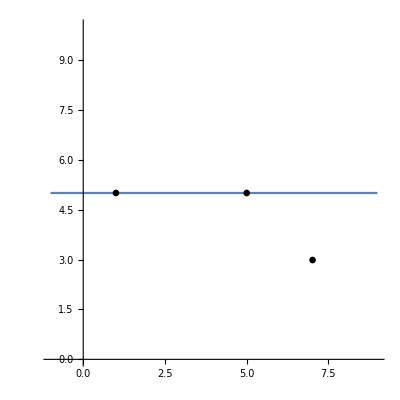

```mathematica
ClearAll["Global`*"];
pA={Ax,Ay}={1, 1};
pB={Bx,By}={5, 5};
pC={Cx,Cy}={7, 3};
nRad=.1;
dA=Graphics[{Black,Disk[pA,nRad]}];
dB=Graphics[{Black,Disk[pB,nRad]}];
dC=Graphics[{Black,Disk[pC,nRad]}];
y1[x_]:=(Ay-By)/(Ax-Bx)(x-Ax)+Ay;
f[x_,y_]:=(Ay-By)(x-Ax)-(Ax-Bx)y+Ay(Ax-Bx);
f[Cx,Cy]
f[Cx,8]

g1=Plot[y1[x],{x,-1,9}];
Show[g1,
dA,dB,dC,
Axes->True,
AspectRatio->Automatic
]
```